```mathematica
Integrate[Exp[-Sqrt[R^2+r^2-2 r R Cos[θ]]/L] r/(R^2+r^2-2 r R Cos[θ])Sin[θ],{θ,0,π},Assumptions->{r>0,R>0,L>0,R>r}]
```

(-ExpIntegralEi[(r-R)/L]+ExpIntegralEi[-(r+R)/L])/R

```mathematica
Series[ExpIntegralEi[x],{x,0,2}]
```

-ⅈ (π Floor[(π+Arg[x])/(2 π)]+(ⅈ (EulerGamma+Log[x])+ⅈ x+(ⅈ x^2)/4+O[x]^3))

```mathematica
N[ExpIntegralEi[-10]]
```

-4.15697×10^-6

```mathematica
FullSimplify[(ⅇ^(-√(r^2-(2 r R)/L+R^2)-√(r^2+(2 r R)/L+R^2)) (ⅇ^(√(r^2+(2 r R)/L+R^2)) (L+√(L (-2 r R+L (r^2+R^2))))-ⅇ^(√(r^2-(2 r R)/L+R^2)) (L+√(L (2 r R+L (r^2+R^2))))))/(r R)]
```

(ⅇ^(-√(r^2-(2 r R)/L+R^2)-√(r^2+(2 r R)/L+R^2)) (ⅇ^(√(r^2+(2 r R)/L+R^2)) (L+√(L (-2 r R+L (r^2+R^2))))-ⅇ^(√(r^2-(2 r R)/L+R^2)) (L+√(L (2 r R+L (r^2+R^2))))))/(r R)

```mathematica
Series[Sqrt[a-x],{x,Infinity,4}]
```

ⅈ √x-1/2 ⅈ a √(1/x)-1/8 ⅈ a^2 (1/x)^(3/2)-1/16 ⅈ a^3 (1/x)^(5/2)-5/128 ⅈ a^4 (1/x)^(7/2)+O[1/x]^(9/2)

```mathematica
FullSimplify[Normal[Series[Integrate[(-ExpIntegralEi[(r-R)/L]+ExpIntegralEi[-(r+R)/L])/R,{r,0,R}],{R,Infinity,2}]]]
```

(L (ⅇ^(-(2 R)/L) (L-4 ⅇ^(R/L) L)+2 R))/(2 R^2)

```mathematica
Series[ExpIntegralEi[x],{x,0,4}]
```

-ⅈ (π Floor[(π+Arg[x])/(2 π)]+(ⅈ (EulerGamma+Log[x])+ⅈ x+(ⅈ x^2)/4+(ⅈ x^3)/18+(ⅈ x^4)/96+O[x]^5))

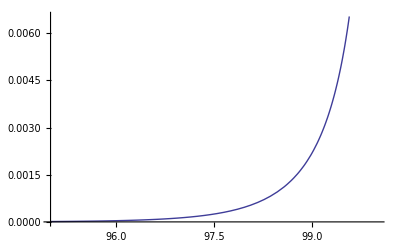

```mathematica
Plot[((-ExpIntegralEi[(r-R)/L]+ExpIntegralEi[-(r+R)/L])/R) /. R->100 /. L -> 1,{r,95,100}]
```

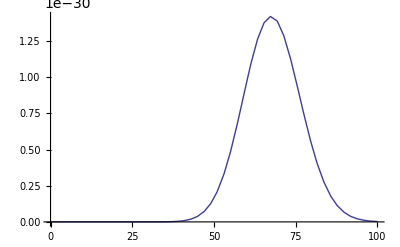

```mathematica
Plot[((ⅇ^(-(r R √(L/(r^2+R^2))+√(L (r^2+R^2)))/L) (-1+ⅇ^((2 r R)/(√(L (r^2+R^2))))) √(L (r^2+R^2)))/(r R)) /. R->100 /. L ->1, {r,0,100}]
```